Project root: /Users/njblost/GitHub/Non-Abelian-Wilczek-Zee-holonomy-calibration-and-feed-forward-for-time-bin-qudits

Tables path:  /Users/njblost/GitHub/Non-Abelian-Wilczek-Zee-holonomy-calibration-and-feed-forward-for-time-bin-qudits/results/tables

Figures path: /Users/njblost/GitHub/Non-Abelian-Wilczek-Zee-holonomy-calibration-and-feed-forward-for-time-bin-qudits/results/figs

Logs path:    /Users/njblost/GitHub/Non-Abelian-Wilczek-Zee-holonomy-calibration-and-feed-forward-for-time-bin-qudits/results/logs

<|reference_unitarity_error→5.34741×10^-8,reference_eigenphases→{-0.701342,0.701342},reference_wilson_traces_r1_r2_r3→{1.52795+0. ⅈ,0.334645+0. ⅈ,-1.01663+0. ⅈ}|>

N | frobenius_error_to_continuum_reference | unitarity_error | eigenphases | wilson_traces_r1_r2_r3
10 | 0.0156618 | 6.38981×10^-16 | {-0.710409,0.710409} | {1.51619+5.55112×10^-17 ⅈ,0.298832+2.77556×10^-16 ⅈ,-1.0631+4.996×10^-16 ⅈ}
20 | 0.00377256 | 2.31289×10^-15 | {-0.703602,0.703602} | {1.52503-1.66533×10^-16 ⅈ,0.325726-2.77556×10^-16 ⅈ,-1.02829-5.55112×10^-17 ⅈ}
40 | 0.000935724 | 2.71523×10^-15 | {-0.701906,0.701906} | {1.52723+3.33067×10^-16 ⅈ,0.332418+1.22125×10^-15 ⅈ,-1.01955+1.88738×10^-15 ⅈ}
80 | 0.000233478 | 6.43163×10^-15 | {-0.701483,0.701483} | {1.52777-3.88578×10^-16 ⅈ,0.334088-2.44249×10^-15 ⅈ,-1.01736-4.38538×10^-15 ⅈ}
160 | 0.0000583328 | 4.64307×10^-15 | {-0.701377,0.701377} | {1.52791-2.22045×10^-16 ⅈ,0.334505-1.66533×10^-16 ⅈ,-1.01682+2.77556×10^-16 ⅈ}
320 | 0.0000145721 | 1.35768×10^-14 | {-0.70135,0.70135} | {1.52794-2.38698×10^-15 ⅈ,0.33461-7.21645×10^-15 ⅈ,-1.01668-9.32587×10^-15 ⅈ}
640 | 3.63392×10^-6 | 1.75654×10^-14 | {-0.701344,0.701344} | {1.52795-7.82707×10^-15 ⅈ,0.334636-2.15383×10^-14 ⅈ,-1.01664-2.58682×10^-14 ⅈ}
1280 | 9.00881×10^-7 | 3.24808×10^-14 | {-0.701342,0.701342} | {1.52795+1.38778×10^-15 ⅈ,0.334642+4.4964×10^-15 ⅈ,-1.01664+6.10623×10^-15 ⅈ}

N | frobenius_error_to_continuum_reference | unitarity_error
10 | 0.0156618 | 6.38981×10^-16
20 | 0.00377256 | 2.31289×10^-15
40 | 0.000935724 | 2.71523×10^-15
80 | 0.000233478 | 6.43163×10^-15
160 | 0.0000583328 | 4.64307×10^-15
320 | 0.0000145721 | 1.35768×10^-14
640 | 3.63392×10^-6 | 1.75654×10^-14
1280 | 9.00881×10^-7 | 3.24808×10^-14

<|log_log_fit_intercept→0.446849,log_log_fit_slope→-2.00849,estimated_order→2.00849|>

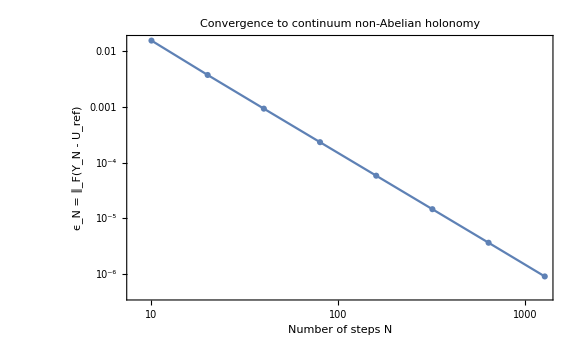

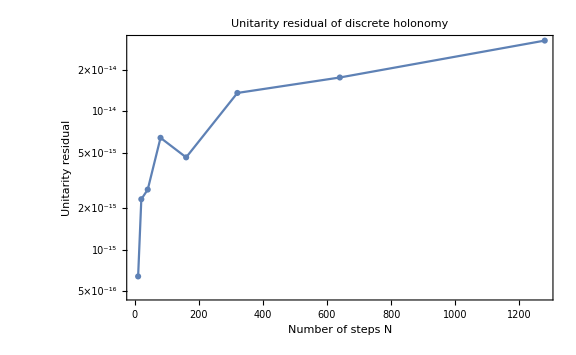

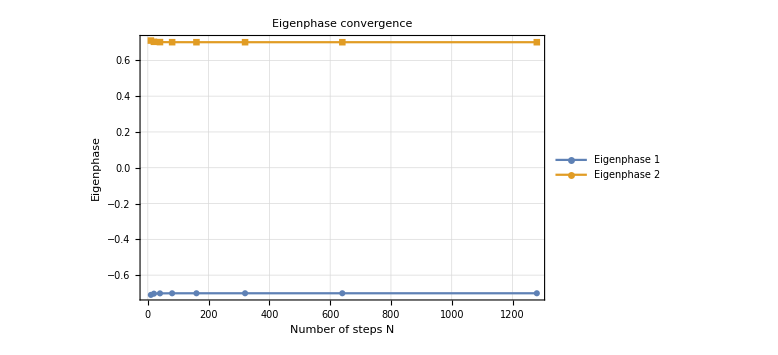

02_nonabelian_convergence.nb completed.

Purpose:
Validate convergence of the discrete ordered-product holonomy estimator against a continuum reference solution.

Synthetic connection:
A(t) = i [0.7 cos(t) sigma_x + 0.4 sin(2 t) sigma_y + 0.2 sigma_z].

Continuum equation:
U'(t) = -A(t) U(t), U(0) = I.

Expected behavior:
Frobenius error to the continuum reference should decrease under mesh refinement.
Unitarity residual should remain near machine precision.
Eigenphases should stabilize as N increases.

Log-log fit:
slope = -2.00849
estimated order = 2.00849

Reference diagnostics:
<|"reference_unitarity_error" -> 5.347411632239695*^-8, "reference_eigenphases" -> {-0.7013416583093254, 0.7013416583093254}, "reference_wilson_traces_r1_r2_r3" -> {1.5279543294222593 + 0.*I, 0.33464450842404625 + 0.*I, -1.0166327461834823 + 0.*I}|>

Generated files:
/Users/njblost/GitHub/Non-Abelian-Wilczek-Zee-holonomy-calibration-and-feed-forward-for-time-bin-qudits/results/tables/02_nonabelian_convergence.csv
/Users/njblost/GitHub/Non-Abelian-Wilczek-Zee-holonomy-calibration-and-feed-forward-for-time-bin-qudits/results/tables/02_nonabelian_convergence_numeric.csv
/Users/njblost/GitHub/Non-Abelian-Wilczek-Zee-holonomy-calibration-and-feed-forward-for-time-bin-qudits/results/tables/02_nonabelian_eigenphase_convergence.csv
/Users/njblost/GitHub/Non-Abelian-Wilczek-Zee-holonomy-calibration-and-feed-forward-for-time-bin-qudits/results/figs/02_nonabelian_convergence.pdf
/Users/njblost/GitHub/Non-Abelian-Wilczek-Zee-holonomy-calibration-and-feed-forward-for-time-bin-qudits/results/figs/02_nonabelian_convergence.png
/Users/njblost/GitHub/Non-Abelian-Wilczek-Zee-holonomy-calibration-and-feed-forward-for-time-bin-qudits/results/figs/02_nonabelian_unitarity.pdf
/Users/njblost/GitHub/Non-Abelian-Wilczek-Zee-holonomy-calibration-and-feed-forward-for-time-bin-qudits/results/figs/02_nonabelian_unitarity.png
/Users/njblost/GitHub/Non-Abelian-Wilczek-Zee-holonomy-calibration-and-feed-forward-for-time-bin-qudits/results/figs/02_nonabelian_eigenphase_convergence.pdf
/Users/njblost/GitHub/Non-Abelian-Wilczek-Zee-holonomy-calibration-and-feed-forward-for-time-bin-qudits/results/figs/02_nonabelian_eigenphase_convergence.png

Project root:
/Users/njblost/GitHub/Non-Abelian-Wilczek-Zee-holonomy-calibration-and-feed-forward-for-time-bin-qudits

<|reference_unitarity_error→5.34741×10^-8,max_discrete_unitarity_error→3.24808×10^-14,initial_convergence_error→0.0156618,final_convergence_error→9.00881×10^-7,estimated_order→2.00849,full_csv→/Users/njblost/GitHub/Non-Abelian-Wilczek-Zee-holonomy-calibration-and-feed-forward-for-time-bin-qudits/results/tables/02_nonabelian_convergence.csv,numeric_csv→/Users/njblost/GitHub/Non-Abelian-Wilczek-Zee-holonomy-calibration-and-feed-forward-for-time-bin-qudits/results/tables/02_nonabelian_convergence_numeric.csv,phase_csv→/Users/njblost/GitHub/Non-Abelian-Wilczek-Zee-holonomy-calibration-and-feed-forward-for-time-bin-qudits/results/tables/02_nonabelian_eigenphase_convergence.csv,convergence_plot_pdf→/Users/njblost/GitHub/Non-Abelian-Wilczek-Zee-holonomy-calibration-and-feed-forward-for-time-bin-qudits/results/figs/02_nonabelian_convergence.pdf,unitarity_plot_pdf→/Users/njblost/GitHub/Non-Abelian-Wilczek-Zee-holonomy-calibration-and-feed-forward-for-time-bin-qudits/results/figs/02_nonabelian_unitarity.pdf,phase_plot_pdf→/Users/njblost/GitHub/Non-Abelian-Wilczek-Zee-holonomy-calibration-and-feed-forward-for-time-bin-qudits/results/figs/02_nonabelian_eigenphase_convergence.pdf,log→/Users/njblost/GitHub/Non-Abelian-Wilczek-Zee-holonomy-calibration-and-feed-forward-for-time-bin-qudits/results/logs/02_nonabelian_convergence_log.txt|>

```mathematica
(*02—Non-Abelian Convergence Validation*)(*This notebook validates convergence of the discrete ordered-product holonomy estimator against a continuum reference solution for a synthetic non-Abelian connection.The connection is anti-Hermitian and noncommuting at different parameter values,so path ordering is essential.*)(*Initialization*)
ClearAll["Global`*"];

(*The notebook lives in notebooks/,so the project root is its parent.*)
rootPath=ParentDirectory[NotebookDirectory[]];

(*Load shared tools.Important:HolonomyTools.wl clears Global`*,so paths must be defined again after Get.*)
SetDirectory[rootPath];
Get[FileNameJoin[{rootPath,"src","HolonomyTools.wl"}]];

(*Re-define paths after loading HolonomyTools.wl.*)
rootPath=ParentDirectory[NotebookDirectory[]];
SetDirectory[rootPath];

resultsPath=FileNameJoin[{rootPath,"results"}];
tablesPath=FileNameJoin[{rootPath,"results","tables"}];
figsPath=FileNameJoin[{rootPath,"results","figs"}];
logsPath=FileNameJoin[{rootPath,"results","logs"}];

Do[If[!DirectoryQ[dir],CreateDirectory[dir,CreateIntermediateDirectories->True]],{dir,{resultsPath,tablesPath,figsPath,logsPath}}];

ClearAll[localExportCSV,localExportTXT,localExportFIG];

localExportCSV[name_String,data_]:=Module[{path},path=FileNameJoin[{tablesPath,name}];
Export[path,data,"CSV"];
path];

localExportTXT[name_String,text_String]:=Module[{path},path=FileNameJoin[{logsPath,name}];
Export[path,text,"Text"];
path];

localExportFIG[name_String,fig_]:=Module[{path},path=FileNameJoin[{figsPath,name}];
Export[path,fig];
path];

SeedRandom[23456];

Print["Project root: ",rootPath];
Print["Tables path:  ",tablesPath];
Print["Figures path: ",figsPath];
Print["Logs path:    ",logsPath];

(*Continuum reference holonomy*)

(*The synthetic connection is defined in src/HolonomyTools.wl as:syntheticConnection[t_]=I (0.7 Cos[t] sigmaX+0.4 Sin[2 t] sigmaY+0.2 sigmaZ).*)

Hreference=continuumHolonomy[2 Pi];

referenceDiagnostics=<|"reference_unitarity_error"->unitaryError[Hreference],"reference_eigenphases"->eigenphases[Hreference],"reference_wilson_traces_r1_r2_r3"->wilsonTraces[Hreference,3]|>;

referenceDiagnostics

(*Discrete convergence data*)

nList={10,20,40,80,160,320,640,1280};

convergenceRows=Table[Module[{Hdisc,err,unitErr,phases,traces},Hdisc=discreteFromConnection[nSteps];
err=frobeniusError[Hdisc,Hreference];
unitErr=unitaryError[Hdisc];
phases=eigenphases[Hdisc];
traces=wilsonTraces[Hdisc,3];
{nSteps,err,unitErr,phases,traces}],{nSteps,nList}];

convergenceTable=Prepend[convergenceRows,{"N","frobenius_error_to_continuum_reference","unitarity_error","eigenphases","wilson_traces_r1_r2_r3"}];

Grid[convergenceTable,Frame->All,Alignment->Left,ItemSize->All]

(*Numeric table for plotting and regression*)

convergenceNumericRows=convergenceRows[[All,{1,2,3}]];

convergenceNumericTable=Prepend[convergenceNumericRows,{"N","frobenius_error_to_continuum_reference","unitarity_error"}];

Grid[convergenceNumericTable,Frame->All,Alignment->Left,ItemSize->All]

(*Estimate convergence slope*)

(*For a log-log convergence plot,fit log(error)=a+b log(N).A negative slope indicates convergence.For midpoint exponentials,the observed order may be close to second order for this smooth benchmark,even though the general first-order polar-overlap theorem gives a conservative guarantee.*)

fitData=({Log[#[[1]]],Log[#[[2]]]}&/@convergenceNumericRows);

linearFit=LinearModelFit[fitData,x,x];

convergenceSlope=linearFit["BestFitParameters"][[2]];

fitSummary=<|"log_log_fit_intercept"->linearFit["BestFitParameters"][[1]],"log_log_fit_slope"->convergenceSlope,"estimated_order"->-convergenceSlope|>;

fitSummary

(*Plot:convergence error*)

convergencePlot=ListLogLogPlot[convergenceNumericRows[[All,{1,2}]],Joined->True,PlotMarkers->Automatic,Frame->True,FrameLabel->{"Number of steps N","\!\(\*SubscriptBox[\(ϵ\), \(N\)]\) = \!\(\*SubscriptBox[\(∥\), \(F\)]\)(\!\(\*SubscriptBox[\(Υ\), \(N\)]\) - \!\(\*SubscriptBox[\(U\), \(ref\)]\))"},GridLines->Automatic,ImageSize->Large,PlotLabel->"Convergence to continuum non-Abelian holonomy"];

convergencePlot

(*Plot:unitarity residual*)

unitarityPlot=ListLogPlot[convergenceNumericRows[[All,{1,3}]],Joined->True,PlotMarkers->Automatic,Frame->True,FrameLabel->{"Number of steps N","Unitarity residual"},GridLines->Automatic,ImageSize->Large,PlotLabel->"Unitarity residual of discrete holonomy"];

unitarityPlot

(*Plot:eigenphase convergence*)

phaseRows=Table[Module[{phases},phases=convergenceRows[[j,4]];
{convergenceRows[[j,1]],phases[[1]],phases[[2]]}],{j,Length[convergenceRows]}];

phaseTable=Prepend[phaseRows,{"N","eigenphase_1","eigenphase_2"}];

phasePlot=ListLinePlot[{phaseRows[[All,{1,2}]],phaseRows[[All,{1,3}]]},Joined->True,PlotMarkers->Automatic,Frame->True,FrameLabel->{"Number of steps N","Eigenphase"},PlotLegends->{"Eigenphase 1","Eigenphase 2"},GridLines->Automatic,ImageSize->Large,PlotLabel->"Eigenphase convergence"];

phasePlot

(*Export results*)

csvPathFull=localExportCSV["02_nonabelian_convergence.csv",convergenceTable];

csvPathNumeric=localExportCSV["02_nonabelian_convergence_numeric.csv",convergenceNumericTable];

csvPathPhases=localExportCSV["02_nonabelian_eigenphase_convergence.csv",phaseTable];

figPathConvergencePDF=localExportFIG["02_nonabelian_convergence.pdf",convergencePlot];

figPathConvergencePNG=localExportFIG["02_nonabelian_convergence.png",convergencePlot];

figPathUnitarityPDF=localExportFIG["02_nonabelian_unitarity.pdf",unitarityPlot];

figPathUnitarityPNG=localExportFIG["02_nonabelian_unitarity.png",unitarityPlot];

figPathPhasesPDF=localExportFIG["02_nonabelian_eigenphase_convergence.pdf",phasePlot];

figPathPhasesPNG=localExportFIG["02_nonabelian_eigenphase_convergence.png",phasePlot];

logText=StringRiffle[{"02_nonabelian_convergence.nb completed.","","Purpose:","Validate convergence of the discrete ordered-product holonomy estimator against a continuum reference solution.","","Synthetic connection:","A(t) = i [0.7 cos(t) sigma_x + 0.4 sin(2 t) sigma_y + 0.2 sigma_z].","","Continuum equation:","U'(t) = -A(t) U(t), U(0) = I.","","Expected behavior:","Frobenius error to the continuum reference should decrease under mesh refinement.","Unitarity residual should remain near machine precision.","Eigenphases should stabilize as N increases.","","Log-log fit:","slope = "<>ToString[convergenceSlope],"estimated order = "<>ToString[-convergenceSlope],"","Reference diagnostics:",ToString[referenceDiagnostics,InputForm],"","Generated files:",csvPathFull,csvPathNumeric,csvPathPhases,figPathConvergencePDF,figPathConvergencePNG,figPathUnitarityPDF,figPathUnitarityPNG,figPathPhasesPDF,figPathPhasesPNG,"","Project root:",rootPath},"\n"];

logPath=localExportTXT["02_nonabelian_convergence_log.txt",logText];

Print[logText];

(*Final validation summary*)

summary=<|"reference_unitarity_error"->referenceDiagnostics["reference_unitarity_error"],"max_discrete_unitarity_error"->Max[convergenceRows[[All,3]]],"initial_convergence_error"->convergenceRows[[1,2]],"final_convergence_error"->convergenceRows[[-1,2]],"estimated_order"->-convergenceSlope,"full_csv"->csvPathFull,"numeric_csv"->csvPathNumeric,"phase_csv"->csvPathPhases,"convergence_plot_pdf"->figPathConvergencePDF,"unitarity_plot_pdf"->figPathUnitarityPDF,"phase_plot_pdf"->figPathPhasesPDF,"log"->logPath|>;

summary
```